### Setup

Function for a custom plot style.

```mathematica
customplot[path_,color_]:=Block[{},
Show[
Graphics[
Table[
{Thickness[0.01],color[(i-1)/20],Line[path[[i;;i+1]]]}
,{i,1,Length[path]-1}]
]
,Frame->True,PlotRange->{{-6,0},{-2.,0}},ImageSize->Large,FrameTicksStyle->Directive[Black,22],FrameLabel->{Style["Log10 Size",22,Black],Style["Log 1-Circularity",22,Black]},AspectRatio->1]
]
```

#### Define Colormaps

```mathematica
CIRCCOLORMAP=(Blend[{{0.25964,RGBColor[78/255,103/255,155/255]},{0.43633,RGBColor[91/255,147/255,178/255]},{0.60460,RGBColor[84/255,209/255,185/255]},{0.78540,RGBColor[179/255,224/255,144/255]},{0.86481,RGBColor[228/255,244/255,115/255]},{0.90690,RGBColor[255/255,255/255,180/255]},{1.0,RGBColor[255/255,255/255,255/255]}},#]&);
```

```mathematica
areamap=(Blend[{{0.1,RGBColor[1,0.93,0.7]},
{0.05,RGBColor[225/255.,202/255.,84/255.]},
{0.01,RGBColor[218/255.,153/255.,55/255.]},
{0.005,RGBColor[227/255.,79/255.,59/255.]},
{0.001,RGBColor[118/255.,52/255.,141/255.]},
{0.0005,RGBColor[60/255.,39/255.,164/255.]},
{0.0001,Black}},#]&);
```

### Define Function to Polygonize the data and return the edge locations.

```mathematica
GETEDGES[data_]:=Block[{},
bin=Clip[data,{0,1}];nzs=Position[bin,1];XXS=DeleteDuplicates[nzs[[All,2]]];DELTAX=Max[XXS]-Min[XXS];edges=ParallelTable[
Table[
me=data[[i]][[j]];
If[me≠data[[i+1]][[j]]||me≠data[[i-1]][[j]]||me≠data[[i]][[j+1]]||me≠data[[i]][[j-1]],
{i,j}
,
##&[]
]
,{j,2,Length[data[[i]]]-1}]
,{i,2,Length[data]-1}];
Print[Colorize[data,ImageSize->400]];
neighbors=ComponentMeasurements[data,"Neighbors"];
dims=Dimensions[data];
verts=ParallelTable[
Table[
If[Length[DeleteDuplicates[{data[[i-1]][[j-1]],data[[i-1]][[j]],data[[i-1]][[j+1]],data[[i]][[j-1]],data[[i]][[j]],data[[i]][[j+1]],data[[i+1]][[j-1]],data[[i+1]][[j-1]],data[[i+1]][[j]]}]]>2,{j,dims[[1]]-i},##&[]]
,{j,2,dims[[2]]-1}]
,{i,2,dims[[1]]-1}];
verts2=ParallelTable[
Table[
If[Length[DeleteDuplicates[{data[[i-1]][[j-1]],data[[i-1]][[j]],data[[i-1]][[j+1]],data[[i]][[j-1]],data[[i]][[j]],data[[i]][[j+1]],data[[i+1]][[j-1]],data[[i+1]][[j-1]],data[[i+1]][[j]]}]]>2,{{j,dims[[1]]-i},DeleteDuplicates[{data[[i-1]][[j-1]],data[[i-1]][[j]],data[[i-1]][[j+1]],data[[i]][[j-1]],data[[i]][[j]],data[[i]][[j+1]],data[[i+1]][[j-1]],data[[i+1]][[j-1]],data[[i+1]][[j]]}]},##&[]]
,{j,2,dims[[2]]-1}]
,{i,2,dims[[1]]-1}];
verts=Partition[Flatten[verts],2];
check=1;
flag=True;
While[flag==True,
ds=1.Table[Norm[verts[[check]]-verts[[o]]],{o,1,Length[verts]}];
(*todel=Position[ds,_?(0<#≤5&)];*)
todel=Position[ds,_?(0<#≤3.5&)];
verts=Delete[verts,todel];
If[check==Length[verts],flag=False;Break;];
check++;
];
{d1,d2}=Dimensions[data];
todo=DeleteDuplicates[Flatten[data]];
ALLEDGES=ParallelTable[
Print["I am doing: "<>ToString[pp]<>" out of "<>ToString[Length[todo]]];
sil=Table[
Table[
If[data[[i]][[j]]==todo[[pp]],1,0]
,{j,1,d2}]
,{i,1,d1}];
If[Length[Position[sil,1]]>1,
silhoutte=MorphologicalPerimeter[sil];
set=ContourBasedFeature[silhoutte];
set=Reverse[set,2];
set=Table[{set[[o]][[1]],d1-set[[o]][[2]]},{o,1,Length[set]}];
set2=Reverse[set,2];
verts2=Reverse[verts,2];
points=Table[
(*Table[If[1.Norm[set[[p]]-verts[[o]]]≤4.5,verts[[o]],##&[]]*)
Table[If[1.Norm[set[[p]]-verts[[o]]]≤3.5,verts[[o]],##&[]]
,{o,1,Length[verts]}]
,{p,1,Length[set]}];
points=Partition[Flatten[points],2];
points=DeleteDuplicates[points];
points
,
##&[]
]
,{pp,2,Length[todo]}];
allverts=DeleteDuplicates[Partition[Flatten[ALLEDGES],2]];
Return[ALLEDGES];
]
```

Function the create the polygon for a single label.

```mathematica
ContourBasedFeature[silhouette_]:=Module[{centroid,startpoint,positions,contourPoints,order,clockwiseorder},(centroid=ComponentMeasurements[silhouette,"Centroid"][[All,2]]//Flatten;
positions=Position[silhouette,1];
startpoint=Select[positions,#[[2]]==Ceiling[centroid[[2]]]&&#[[1]]<Ceiling[centroid[[1]]]&];
contourPoints=Join[startpoint,DeleteCases[positions,startpoint//Flatten]];
order=contourPoints[[Last@FindShortestTour[contourPoints]]];
If[order[[1,2]]>order[[2,2]],Join[{order[[1]]},order[[Range[Length[order],2,-1]]]],order])]
```

### Neuroptera

```mathematica
ALLEDGES=1.ToExpression[Import["./Lloyd_Wing_Neuroptera_LR/Neuroptera_Edges2.csv","Data"]];
ALLEDGES=Table[Partition[ALLEDGES[[i]],2],{i,1,Length[ALLEDGES]}];
```

```mathematica
ALLEDGES[[1]]
```

{{2504.,1013.},{2441.,900.},{2387.,899.},{2449.,1012.}}

```mathematica
(*ALLEDGES=1.Table[Partition[ALLEDGES[[j]],2],{j,1,Length[ALLEDGES]}];*)
allflat=Partition[Flatten[ALLEDGES],2];
```

```mathematica
mea=Mean[allflat]1.;
ALLC=Table[
Table[
ALLEDGES[[o]][[n]]-mea
,{n,1,Length[ALLEDGES[[o]]]}]
,{o,1,Length[ALLEDGES]}];
ALLC=Table[
If[Length[ALLC[[m]]]>2,ALLC[[m]],##&[]]
,{m,1,Length[ALLC]}];
ALLEDGES=ALLC;
ALLEDGES=Table[
Table[
ALLEDGES[[n]][[j]]+0.0001{RandomReal[{-1,1}],RandomReal[{-1,1}]}
,{j,1,Length[ALLEDGES[[n]]]}]
,{n,1,Length[ALLEDGES]}];
```

Check if the points are colinear

```mathematica
col[pts_]:=Module[{a},a=MapThread[Append,{pts,ConstantArray[1,Length[pts]]}];
If[Length[NullSpace[a]]==Last[Dimensions[pts]]-1,Sort[pts][[{1,-1}]],pts]]
```

```mathematica
ALLEDGES=Table[
If[Length[col[ALLEDGES[[n]]]]>2,MeshPrimitives[ConvexHullMesh[
ALLEDGES[[n]]]
,2][[1]][[1]],##&[]]
,{n,1,Length[ALLEDGES]}];
ALLEDGES=Table[
If[
Length[DeleteDuplicates[ALLEDGES[[mn]]]]>2&&Length[DeleteDuplicates[ALLEDGES[[mn]][[All,1]]]]>=2&&Length[DeleteDuplicates[ALLEDGES[[mn]][[All,2]]]]>=2
,ALLEDGES[[mn]],##&[]]
,{mn,1,Length[ALLEDGES]}];
rm=Total[Table[
Area[ConvexHullMesh[ALLEDGES[[jj]]]]
,{jj,1,Length[ALLEDGES]}]];
POLYS=ALLEDGES;
Len=Sqrt[rm]
```

1658.57

```mathematica
forpca=1.Partition[Flatten[POLYS],2];
ppp=Position[forpca[[All,1]],Max[forpca[[All,1]]]];
pca=PrincipalComponents[forpca];
leng=Max[pca[[All,1]]]-Min[pca[[All,1]]];
{Xs,Ys}=Transpose[pca];
If[Xs[[ppp[[1]][[1]]]]<0,Xs=-Xs];
pca=Transpose[{Xs,Ys}];
len=Table[
Length[POLYS[[j]]]
,{j,1,Length[POLYS]}];
Acc=Join[{0},Accumulate[len]];
POLYS=Table[
pca[[Acc[[nn]]+1;;Acc[[nn+1]]]]
,{nn,1,Length[Acc]-1}];
ALLEDGES=POLYS;
ALLEDGES=Table[
If[
Length[DeleteDuplicates[ALLEDGES[[mn]]]]>2&&Length[DeleteDuplicates[ALLEDGES[[mn]][[All,1]]]]>2&&Length[DeleteDuplicates[ALLEDGES[[mn]][[All,2]]]]>2
,ALLEDGES[[mn]],##&[]]
,{mn,1,Length[ALLEDGES]}];
CHS=Table[
ConvexHullMesh[Round[ALLEDGES[[jj]],0.0001]]
,{jj,1,Length[ALLEDGES]}];
CHS2=Table[
If[RegionDimension[CHS[[n]]]==2,CHS[[n]],##&[]]
,{n,1,Length[CHS]}];
Clear[x];Clear[y];
allverts=DeleteDuplicates[Partition[Flatten[ALLEDGES],2]];
vertmatrix=Table[0,{Length[allverts]},{Length[allverts]}];
For[x=1,x≤Length[ALLEDGES],x++,
back=ALLEDGES[[x]][[-1]];
front=ALLEDGES[[x]][[1]];
true=Partition[Flatten[{back,ALLEDGES[[x]],front}],2];
For[y=2,y≤Length[true]-1,y++,
left=true[[y-1]];
me=true[[y]];
right=true[[y+1]];
leftp=Flatten[Position[allverts,left]][[1]];
truep=Flatten[Position[allverts,me]][[1]];
rightp=Flatten[Position[allverts,right]][[1]];
vertmatrix[[truep]][[leftp]]=1;
vertmatrix[[truep]][[rightp]]=1;
];
];
weighted=vertmatrix;
ps=Position[weighted,1];
Table[
do=ps[[v]];
d1=allverts[[do[[1]]]];
d2=allverts[[do[[2]]]];
weighted[[do[[1]]]][[do[[2]]]]=(*1/*)(Norm[d1-d2](*+10^-10*));
,{v,1,Length[ps]}];
INSIDE=Total[Total[weighted]]/2;
tocheck={INSIDE,Length[CHS2]};
ALLEDGES=POLYS;
ALLEDGES=Table[
If[
Length[DeleteDuplicates[ALLEDGES[[mn]]]]>2&&Length[DeleteDuplicates[ALLEDGES[[mn]][[All,1]]]]>2&&Length[DeleteDuplicates[ALLEDGES[[mn]][[All,2]]]]>2
,ALLEDGES[[mn]],##&[]]
,{mn,1,Length[ALLEDGES]}];
rm=Total[Table[
Area[ConvexHullMesh[ALLEDGES[[jj]]]]
,{jj,1,Length[ALLEDGES]}]];
CHS=Table[
ConvexHullMesh[Round[ALLEDGES[[jj]],0.0001]]
,{jj,1,Length[ALLEDGES]}];
CHS2=Table[
If[RegionDimension[CHS[[n]]]==2,CHS[[n]],##&[]]
,{n,1,Length[CHS]}];
NormalizeA=True;
forpca=1.Partition[Flatten[POLYS],2];
ppp=Position[forpca[[All,1]],Max[forpca[[All,1]]]];
pca=PrincipalComponents[forpca];
leng=Max[pca[[All,1]]]-Min[pca[[All,1]]];
{Xs,Ys}=Transpose[pca];
If[NormalizeA==True,Xs=Xs/Len;Ys=Ys/Len;];
If[Xs[[ppp[[1]][[1]]]]<0,Xs=-Xs];
pca=Transpose[{Xs,Ys}];
len=Table[
Length[POLYS[[j]]]
,{j,1,Length[POLYS]}];
Acc=Join[{0},Accumulate[len]];
POLYS=Table[
pca[[Acc[[nn]]+1;;Acc[[nn+1]]]]
,{nn,1,Length[Acc]-1}];
ALLEDGES=POLYS;
ALLEDGES=Table[
If[
Length[DeleteDuplicates[ALLEDGES[[mn]]]]>2&&Length[DeleteDuplicates[ALLEDGES[[mn]][[All,1]]]]>2&&Length[DeleteDuplicates[ALLEDGES[[mn]][[All,2]]]]>2
,ALLEDGES[[mn]],##&[]]
,{mn,1,Length[ALLEDGES]}];
rm=Total[Table[
Area[ConvexHullMesh[ALLEDGES[[jj]]]]
,{jj,1,Length[ALLEDGES]}]];
CHS=Table[
ConvexHullMesh[Round[ALLEDGES[[jj]],0.0001]]
,{jj,1,Length[ALLEDGES]}];
CHS2=Table[
If[RegionDimension[CHS[[n]]]==2,CHS[[n]],##&[]]
,{n,1,Length[CHS]}];
```

### Get the union of all shapes

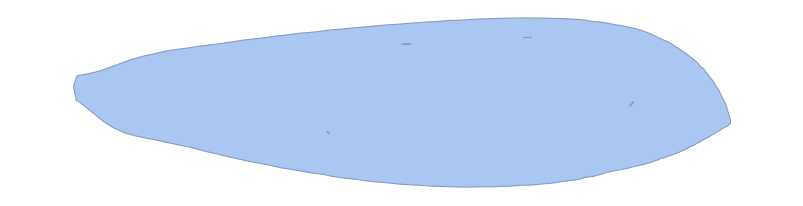

```mathematica
regionunion=RegionUnion[CHS2];
boundd=BoundaryDiscretizeRegion[regionunion]
```

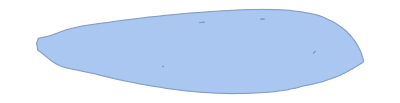

```mathematica
mesh=BoundaryMesh[regionunion]
```

### Get the perimiter

```mathematica
perimiter=Perimeter[boundd]
```

4.97806

```mathematica
Clear[x];Clear[y];
allverts=DeleteDuplicates[Partition[Flatten[ALLEDGES],2]];
vertmatrix=Table[0,{Length[allverts]},{Length[allverts]}];
For[x=1,x≤Length[ALLEDGES],x++,
back=ALLEDGES[[x]][[-1]];
front=ALLEDGES[[x]][[1]];
true=Partition[Flatten[{back,ALLEDGES[[x]],front}],2];
For[y=2,y≤Length[true]-1,y++,
left=true[[y-1]];
me=true[[y]];
right=true[[y+1]];
leftp=Flatten[Position[allverts,left]][[1]];
truep=Flatten[Position[allverts,me]][[1]];
rightp=Flatten[Position[allverts,right]][[1]];
vertmatrix[[truep]][[leftp]]=1;
vertmatrix[[truep]][[rightp]]=1;
];
];
```

### Output for the manuscript.

Show shape, Perimeter, internal network length, number of polygons

```mathematica
weighted=vertmatrix;
ps=Position[weighted,1];
Table[
do=ps[[v]];
d1=allverts[[do[[1]]]];
d2=allverts[[do[[2]]]];
weighted[[do[[1]]]][[do[[2]]]]=(*1/*)(Norm[d1-d2](*+10^-10*));
,{v,1,Length[ps]}];
INSIDE=Total[Total[weighted]]/2;
tocheck={boundd,perimiter,INSIDE,Length[CHS2]}
```

{-Graphics-,4.97806,96.2179,475}

```mathematica
POLYS=Table[
(*1.Partition[ALLEDGES[[i]],2]*)
ALLEDGES[[i]]1.
,{i,1,Length[ALLEDGES]}];
```

Compute circularity of each polygon for plotting.

```mathematica
CIRC=Table[
poly=Polygon[POLYS[[xx]]];
AREA=Area[poly];
Trueperimiter=RegionMeasure[RegionBoundary[poly]];
Rcirc=Trueperimiter/(2π);
AreaC=Rcirc^2 π;
circularity=AREA/AreaC
,{xx,1,Length[POLYS]}];
```

```mathematica
Graphics[{
Table[
{White,EdgeForm[Directive[Thickness[0.01/3]]],Polygon[
ALLEDGES[[h]]
]}
,{h,1,Length[ALLEDGES]}]
,
Table[
{RGBColor[0.25,0.5,0.91],Disk[allverts[[h]],0.001]}
,{h,1,Length[allverts]}]
}
]
```

-Graphics-

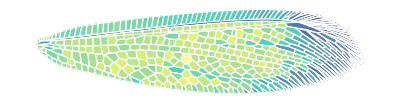

```mathematica
Graphics[
Table[
{CIRCCOLORMAP[CIRC[[h]]],EdgeForm[Directive[Thickness[0.002],White]],Polygon[
ALLEDGES[[h]]
]}
,{h,1,Length[ALLEDGES]}]
]
```

Compute area of each polygon for plotting.

```mathematica
AREAS=Table[
poly=Polygon[POLYS[[xx]]];
AREA=Area[poly];
AREA
,{xx,1,Length[POLYS]}];
```

```mathematica
areaf=AREAS/Total[AREAS];
```

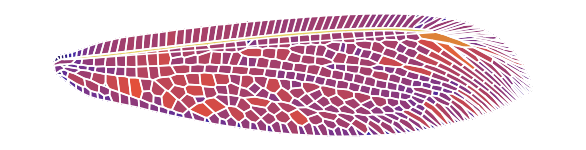

```mathematica
Graphics[
Table[
{areamap[areaf[[h]]],EdgeForm[Directive[Thickness[0.002],White]],Polygon[
ALLEDGES[[h]]
]}
,{h,1,Length[ALLEDGES]}]
]
```

### Read data in from a processed file

Here we assume we will read in the data from an edges file

```mathematica
ALLEDGES=1.ToExpression[Import["./Neuroptera_Edges2.csv","Data"]];
ALLEDGES=Table[Partition[ALLEDGES[[i]],2],{i,1,Length[ALLEDGES]}];
```

```mathematica
ALLEDGES=Table[
If[Length[ALLEDGES[[n]]]>2,ALLEDGES[[n]],##&[]]
,{n,1,Length[ALLEDGES]}];
```

```mathematica
rm=Total[Table[
Area[ConvexHullMesh[ALLEDGES[[jj]]]]
,{jj,1,Length[ALLEDGES]}]];
POLYS=ALLEDGES;
(*rm=RegionMeasure[ConvexHullMesh[Partition[Flatten[POLYS],2]]];*)
Len=Sqrt[rm];
NormalizeA=True;
forpca=1.Partition[Flatten[POLYS],2];
ppp=Position[forpca[[All,1]],Max[forpca[[All,1]]]];
pca=PrincipalComponents[forpca];
leng=Max[pca[[All,1]]]-Min[pca[[All,1]]];
{Xs,Ys}=Transpose[pca];
If[NormalizeA==True,Xs=Xs/Len;Ys=Ys/Len;];
If[Xs[[ppp[[1]][[1]]]]<0,Xs=-Xs];
pca=Transpose[{Xs,Ys}];
len=Table[
Length[POLYS[[j]]]
,{j,1,Length[POLYS]}];
Acc=Join[{0},Accumulate[len]];
POLYS=Table[
pca[[Acc[[nn]]+1;;Acc[[nn+1]]]]
,{nn,1,Length[Acc]-1}];
ALLEDGES=POLYS;
```

```mathematica
Length[allverts]
```

2495

```mathematica
Clear[x];Clear[y];
```

```mathematica
allverts=DeleteDuplicates[Partition[Flatten[ALLEDGES],2]];
vertmatrix=Table[0,{Length[allverts]},{Length[allverts]}];
For[x=1,x≤Length[ALLEDGES],x++,
back=ALLEDGES[[x]][[-1]];
front=ALLEDGES[[x]][[1]];
true=Partition[Flatten[{back,ALLEDGES[[x]],front}],2];
For[y=2,y≤Length[true]-1,y++,
left=true[[y-1]];
me=true[[y]];
right=true[[y+1]];
leftp=Flatten[Position[allverts,left]][[1]];
truep=Flatten[Position[allverts,me]][[1]];
rightp=Flatten[Position[allverts,right]][[1]];
vertmatrix[[truep]][[leftp]]=1;
vertmatrix[[truep]][[rightp]]=1;
];
];
```

### Perform community detection from modularity graph

```mathematica
communities=FindGraphCommunities[AdjacencyGraph[vertmatrix],Method->{"Modularity"(*,"StopTest"->(Length@#2==10&)*)}];
```

```mathematica
COMMUNITIES=communities;
```

```mathematica
Table[vertmatrix[[i,i]]=0,{i,1,Length[vertmatrix]}];
```

```mathematica
ArrayPlot[vertmatrix,ColorRules->{0->White,1->RGBColor[0.16,0.53,0.89]},PlotRangePadding->None]
```

-Graphics-

Show just a subsection of the community graph

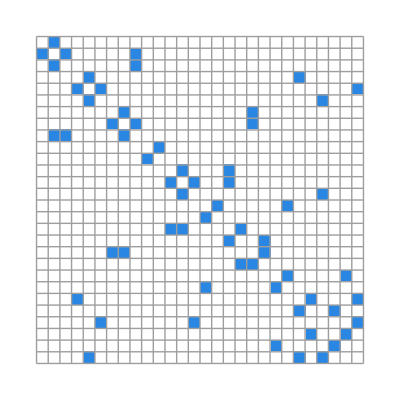

```mathematica
ArrayPlot[vertmatrix[[-28;;,-28;;]],Mesh->True,PlotRangePadding->None,ColorRules->{0->White,1->RGBColor[0.16,0.53,0.89]}]
```

```mathematica
adj=AdjacencyGraph[vertmatrix];
```

```mathematica
c=LocalClusteringCoefficient[adj];
```

```mathematica
Length[communities]
```

17

```mathematica
Table[
Length[communities[[b]]]
,{b,1,Length[communities]}]
```

{94,82,81,81,76,67,60,58,58,54,51,43,39,38,28,26,22}

Color the different communities.

```mathematica
cols=Join[Table[ColorData[10][j],{j,1,11}],Table[ColorData[3][j],{j,1,11}]]
```

{RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196],RGBColor[0.17254901960784313, 0.3607843137254902, 0.07058823529411765],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333],RGBColor[0.22745098039215686, 0.23921568627450981, 0.45098039215686275],RGBColor[0.09803921568627451, 0.06666666666666667, 0.25098039215686274],RGBColor[0.5607843137254902, 0.5254901960784314, 0.5647058823529412],RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],RGBColor[0., 0., 0.]}

```mathematica
clusters=Table[
todo=ALLEDGES[[b]];
RandomSample[Commonest[Table[
p=Flatten[Position[allverts,todo[[n]]]][[1]];
Position[communities,p][[1]][[1]]
,{n,1,Length[todo]}]]][[1]]
,{b,1,Length[ALLEDGES]}];
```

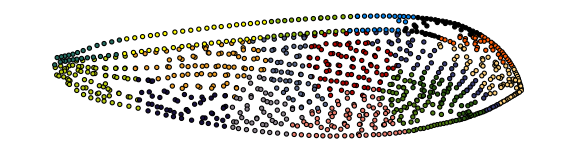

```mathematica
Graphics[
Table[
Table[
{cols[[j]],EdgeForm[Black],Disk[allverts[[communities[[j]][[i]]]],0.01]}
,{i,1,Length[communities[[j]]]}]
,{j,1,Length[communities]}]
,ImageSize->Large]
```

```mathematica
ALLEDGES=1.ToExpression[Import["./Neuroptera_Edges2.csv","Data"]];
ALLEDGES=Table[Partition[ALLEDGES[[i]],2],{i,1,Length[ALLEDGES]}];
```

```mathematica
allflat=Partition[Flatten[ALLEDGES],2];
mea=Mean[allflat]1.;
```

```mathematica
ALLC=Table[
Table[
ALLEDGES[[o]][[n]]-mea
,{n,1,Length[ALLEDGES[[o]]]}]
,{o,1,Length[ALLEDGES]}];
```

```mathematica
ALLC=Table[
If[Length[ALLC[[m]]]>2,ALLC[[m]],##&[]]
,{m,1,Length[ALLC]}];
```

```mathematica
ALLEDGES=ALLC;
```

```mathematica
ALLEDGES=Table[
Table[
ALLEDGES[[n]][[j]]+0.0075{RandomReal[{-1,1}],RandomReal[{-1,1}]}
,{j,1,Length[ALLEDGES[[n]]]}]
,{n,1,Length[ALLEDGES]}];
```

```mathematica
POLYS=Table[
(*1.Partition[ALLEDGES[[i]],2]*)
ALLEDGES[[i]]1.
,{i,1,Length[ALLEDGES]}];
```

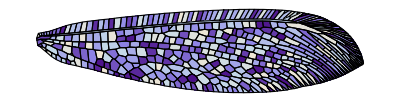

```mathematica
Graphics[
Table[
{ColorData["LakeColors"][RandomReal[]],EdgeForm[Black],Polygon[
ALLEDGES[[h]]
]}
,{h,1,Length[ALLEDGES]}]
]
```

```mathematica
forpca=1.Partition[Flatten[POLYS],2];
ppp=Position[forpca[[All,1]],Max[forpca[[All,1]]]];
pca=PrincipalComponents[forpca];
leng=Max[pca[[All,1]]]-Min[pca[[All,1]]];
{Xs,Ys}=Transpose[pca];
If[Xs[[ppp[[1]][[1]]]]<0,Xs=-Xs];
pca=Transpose[{Xs,Ys}];
```

```mathematica
{xs,ys}=Transpose[ALLEDGES[[15]]];
{Length[DeleteDuplicates[xs]],Length[DeleteDuplicates[ys]]}
```

{4,4}

```mathematica
ALLEDGES[[385]]
```

{{-410.886,-201.213},{-360.892,-261.214},{-313.889,-292.215},{-240.88,-258.217},{-239.889,-246.208},{-298.891,-214.212},{-362.887,-197.22}}

```mathematica
Length[ALLEDGES]
```

475

```mathematica
aas=Table[
RegionMeasure[
Polygon[1.ALLEDGES[[oo]]]
]
,{oo,1,Length[ALLEDGES]}];
```

```mathematica
Dynamic[oo]
```

```mathematica
aas=aas/Total[aas];
```

```mathematica
len=Table[
Length[POLYS[[j]]]
,{j,1,Length[POLYS]}];
Acc=Join[{0},Accumulate[len]];
poly2=Table[
pca[[Acc[[nn]]+1;;Acc[[nn+1]]]]
,{nn,1,Length[Acc]-1}];
```

```mathematica
POLY=Table[
If[
Length[DeleteDuplicates[poly2[[xx]]]]≥3,
DeleteDuplicates[poly2[[xx]]],##&[]
]
,{xx,1,Length[poly2]}];
```

```mathematica
POLY=Table[
chm=ConvexHullMesh[POLY[[z]]];
ordering=MeshCells[chm,2][[1,1]];
out=MeshCoordinates[chm][[ordering]]
,{z,1,Length[POLY]}];
```

```mathematica
AREAS=aas;
```

```mathematica
AREAS=Log10[AREAS];
```

```mathematica
CIRC=Table[
poly=Polygon[POLY[[xx]]];
AREA=Area[poly];
Trueperimiter=RegionMeasure[RegionBoundary[poly]];
Rcirc=Trueperimiter/(2π);
AreaC=Rcirc^2 π;
circularity=AREA/AreaC
,{xx,1,Length[POLY]}];
```

```mathematica
CIRC=1-CIRC;
CIRC=Log[CIRC];
```

```mathematica
bins=Subdivide[Min[pca[[All,1]]],Max[pca[[All,1]]],30];
bins=Table[
bins[[j;;j+1]]
,{j,1,Length[bins]-1}];
```

```mathematica
NUM=200;
```

```mathematica
ymin=Min[pca[[All,2]]];
ymax=Max[pca[[All,2]]];
XYPATH=ParallelTable[
Print[nnn];
getlocalbins=Table[
check=Subdivide[Min[POLY[[oo]][[All,1]]],Max[POLY[[oo]][[All,1]]],1000];
tfs=Table[
If[bins[[nnn]][[1]]<check[[zz]]<bins[[nnn]][[2]],
True,False]
,{zz,1,Length[check]}];
If[MemberQ[tfs,True]==True,True,False]
,{oo,1,Length[POLY]}];
LPs=Position[getlocalbins,True];
POLY2=Extract[POLY,LPs];
AREAS2=Extract[AREAS,LPs];
CIRCS2=Extract[CIRC,LPs];
AREASS=Table[
Total[Table[
If[RegionMember[Polygon[POLY2[[jj]]],RandomPoint[Rectangle[{bins[[nnn]][[1]],ymin},{bins[[nnn]][[2]],ymax}]]]==True,1,0]
,{NUM}]]/(NUM 1.)
,{jj,1,Length[POLY2]}];
AREAF=AREASS/Total[AREASS];
{AREAF.AREAS2,AREAF.CIRCS2}
,{nnn,1,Length[bins]}];
```

28

```mathematica
XYPATH
```

{{-2.91574,-1.06517},{-2.80255,-1.10592},{-2.64054,-1.28249},{-2.56099,-1.37218},{-2.50169,-1.39957},{-2.45789,-1.33733},{-2.46811,-1.40635},{-2.42893,-1.42358},{-2.47528,-1.41338},{-2.42752,-1.33559},{-2.47873,-1.34267},{-2.46103,-1.34419},{-2.51723,-1.30443},{-2.4957,-1.45673},{-2.45931,-1.34026},{-2.51238,-1.32818},{-2.50908,-1.35941},{-2.53361,-1.30246},{-2.54728,-1.36258},{-2.55209,-1.2309},{-2.56472,-1.24766},{-2.60256,-1.24649},{-2.62713,-1.09089},{-2.59425,-0.801549},{-2.57804,-0.647543},{-2.61351,-0.489977},{-2.64629,-0.422439},{-2.73178,-0.381337},{-2.76191,-0.303838},{-3.0457,-0.31785}}

```mathematica
GG=4;
```

```mathematica
XYPATH=Reverse[Transpose[{GaussianFilter[XYPATH[[All,1]],GG],GaussianFilter[XYPATH[[All,2]],GG]}]]
tmp=(Blend[{{0,LightRed},{1,Red}},#]&);
```

{{-2.91911,-0.334095},{-2.83994,-0.358742},{-2.76,-0.402335},{-2.69362,-0.472403},{-2.64636,-0.572609},{-2.61743,-0.700963},{-2.60459,-0.846946},{-2.59594,-0.992234},{-2.58647,-1.11356},{-2.57355,-1.20175},{-2.55947,-1.2591},{-2.54421,-1.29584},{-2.5294,-1.31996},{-2.51635,-1.3349},{-2.50477,-1.34705},{-2.49637,-1.35594},{-2.48977,-1.35768},{-2.48405,-1.35644},{-2.47603,-1.35495},{-2.46745,-1.35944},{-2.4607,-1.36859},{-2.45739,-1.3792},{-2.46002,-1.38743},{-2.47212,-1.38529},{-2.49769,-1.37117},{-2.54189,-1.34433},{-2.6038,-1.30044},{-2.68069,-1.24175},{-2.76014,-1.17904},{-2.82843,-1.12708}}

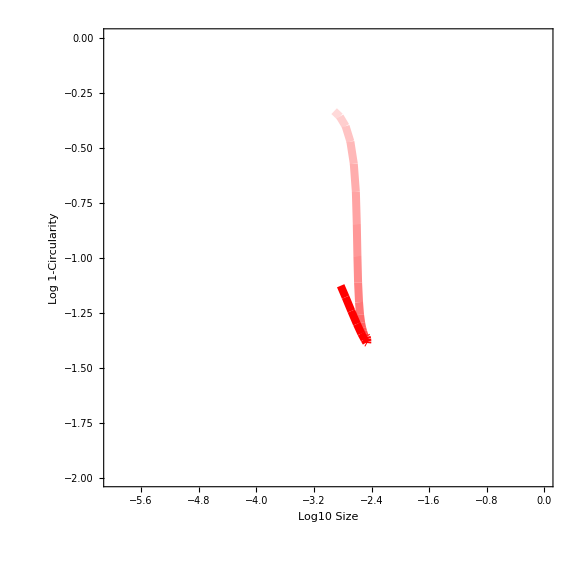

```mathematica
customplot[XYPATH,tmp]
```